## Basis

```mathematica
Needs["NETLink`"];
LoadNETAssembly["NationalInstruments.VisaNS"];
(*"NationalInstruments.VisaNS.TcpipSession" and
 "NationalInstruments.VisaNS.MessageBasedSession" are both okay;
 but the latter can deal with VXI-11, HiSLIP and Socket communication; 
 the former can only deal with VXI-11 protocol. 
For more details, please refer to "SMB100A operating manual"*)

SocketDevices=<||>;
ClearAll[SocketDeviceOpen]
SocketDeviceOpen[ipWithPort_String]:=(SocketDevices[ipWithPort]=NETNew["NationalInstruments.VisaNS.MessageBasedSession","TCPIP::"<>ipWithPort<>"::SOCKET"]);
ClearAll[SocketDeviceClose]
SocketDeviceClose[dev_]:=dev@Dispose[];
SocketDeviceClose[ip_String]:=(SocketDeviceClose@SocketDevices[ip];SocketDevices=Delete[SocketDevices,ip]);
```

## RF (VXI-11 devices)

```mathematica
RFDevices=<||>;
ClearAll[RFDevice]
ClearAll[RFOpen]
ClearAll[RFClose]
ClearAll[RFWrite]
ClearAll[RFRead]
ClearAll[RFFrequency]
ClearAll[RFAmplitude]
ClearAll[RFFrequencyScan]
ClearAll[RFOutput]

RFDevice[dev_?NETLink`NETObjectQ]:=dev;
RFDevice[name_String]:=RFDevices[name];
RFDevice[id_Integer]:=RFDevices⟦id⟧;

RFOpen[ip_String]:=(RFDevices[ip]=NETLink`NETNew["NationalInstruments.VisaNS.MessageBasedSession","TCPIP::"<>ip<>"::INST0::INSTR"]);
RFOpen[id_Integer]:=RFOpen[Keys[RFDevices]⟦id⟧];
RFOpen[]:=(RFOpen/@Keys[RFDevices];);

RFClose[dev_]:=dev@Dispose[];
RFClose[ip_String]:=(RFClose@RFDevices[ip];(*RFDevices=Delete[RFDevices,ip];*));
RFClose[id_Integer]:=(RFClose@RFDevices⟦id⟧;(*RFDevices=Delete[RFDevices,id];*));
RFClose[]:=(RFClose/@Keys[RFDevices];);

RFWrite[dev_,str_String]:=RFDevice[dev]@Write[str(*<>"\n"*)];
RFWrite[dev_,chars_List]:=RFDevice[dev]@Write[chars(*,0,Length[chars]*)];

RFRead[dev_]:=RFDevice[dev]@ReadString[];

RFFrequency[dev_,freq:(_?NumericQ):0]:=Module[{r,d,n},
If[freq===0,
dev@Write["SOURce:FREQuency:CW?\n"];
r=dev@ReadString[];
ToExpression@StringReplace[r,{d:{DigitCharacter,"."}..~~"E"~~n:{DigitCharacter,"+","-"}..:>d<>"*10^"<>n}]/10.^6,
r=StringReplace[ToString[10^6 freq,FortranForm],RegularExpression["([0-9\\.])e([0-9\\+-])"]-> "$1E$2"];
dev@Write["SOURce:FREQuency:CW "<>r<>"\n"];
]];
RFFrequency[ip_String,freq:(_?NumericQ):0]:=RFFrequency[RFDevices[ip],freq];
RFFrequency[id_Integer,freq:(_?NumericQ):0]:=RFFrequency[RFDevices[[id]],freq];

RFAmplitude[dev_,dbm_:"?"]:=Module[{r,d,n},
If[dbm==="?",
dev@Write["SOURce:POWer:POWer?\n"];
r=dev@ReadString[];
ToExpression@StringReplace[r,{d:{DigitCharacter,"."}..~~"E"~~n:{DigitCharacter,"+","-"}..:>d<>"*10^"<>n}],
If[NumberQ@dbm,r=StringReplace[ToString[dbm,FortranForm],RegularExpression["([0-9\\.])e([0-9\\+-])"]-> "$1E$2"];
dev@Write["SOURce:POWer:POWer "<>r<>"\n"],Print["Error"]];
]];
RFAmplitude[ip_String,dbm_:"?"]:=RFAmplitude[RFDevices[ip],dbm];
RFAmplitude[id_Integer,dbm_:"?"]:=RFAmplitude[RFDevices[[id]],dbm];

RFFrequencyScan[dev_,start_?NumericQ,end_?NumericQ,step_?NumericQ]:=Module[{datafile=NewData["RFScan-"],counts="",now},
SequencerAxis[start,end,step];
SequencerData[datafile];
AppendData[datafile, {
{"Sequence",CtrlGetValue@sequencer@"Edit.Sequence.Chapter (us)"<>"\n----------\n"<>CtrlGetValue@sequencer@"Edit.Sequence.Sequence"},
{"Parameter", "Frequency (MHz)"}, 
{"Start", ToString[start]}, 
{"End", ToString[end]}, 
{"Step", ToString[step]}}];
(*Print["RF Frequency Scan Start..."];*)
Monitor[
Do[
If[$Task.Global`stop,Break[],Pause[0.01]];
RFFrequency[dev,now];
counts=counts<>ToString[now]<>" MHz, "<>StringJoin@@Riffle[ToString/@SequencerCounts[]," "]<>"\n";,
{now,start,end,step}],ProgressIndicator[now,{start,end}]];
AppendData[datafile, {{"Counts", counts}}];
(*Print["RF Frequency Scan Finish."];*)
datafile
];

RFOutput[dev_,state_Integer]:=dev@Write["OUTPut "<>ToString[state]<>"\n"];
RFOutput[dev_,True]:=RFOutput[dev,1];
RFOutput[dev_,False]:=RFOutput[dev,0];
RFOutput[ip_String,state_]:=RFOutput[RFDevices[ip],state];
RFOutput[id_Integer,state_]:=RFOutput[RFDevices[[id]],state];
RFOutput[state_]:=(RFOutput[#,state]&/@Values[RFDevices];);
```

## Laser (socket devices)

```mathematica
ClearAll[LaserConnect]
LaserConnect[ipWithPort_String]:=Module[{dev=SocketDeviceOpen[ipWithPort]},dev@TerminationCharacterEnabled=True;
dev@TerminationCharacter=ToCharacterCode[">"][[1]];
dev@DefaultBufferSize=16500;
{dev,dev@ReadString[]}
];

(*以下函数涉及的命令从toptica command manual中找*)
Clear[LaserSignalDisp]
LaserSignalDisp[dev_?NETObjectQ,plotrange_:{-0.02,0.02}]:=Module[{dat,xdat,ydat,a,b},dev@Write["(param-ref 'laser1:scope:data)\n"];
Pause[0.01];
dat=dev@ReadString[];
dat=Partition[Normal@BaseDecode@dat,4098];
dev@Write["(param-ref 'laser1:dl:pc:voltage-set)\n"];
a=ToExpression@StringTake[dev@ReadString[],{2,-3}];
dev@Write["(param-ref 'laser1:scan:amplitude)\n"];
b=ToExpression@StringTake[dev@ReadString[],{2,-3}];
xdat=ImportString[FromCharacterCode[dat[[3,7;;-1]]],"Real32"];
ydat=ImportString[FromCharacterCode[dat[[1,7;;-1]]],"Real32"];
ListLinePlot[{xdat,ydat}ᵀ,PlotRange->{{a-b/2,a+b/2},plotrange},Frame->True,FrameLabel->{"Piezo Voltage (V)","Lock-in Out (V)"},LabelStyle->{Black,Bold},Background->White,GridLines->Automatic]
];

ClearAll[Laser370Connect,Laser935Connect,Laser399Connect,LaserCCSet,LaserPCSet,LaserCCAct,LaserPCAct,LockEnable,LaserScanAmp,ScanEnable,EmissionEnable];

Laser370Connect[]:=(Quiet[laser370@Dispose[]];
laser370=LaserConnect["192.168.32.4::1998"][[1]];)
Laser935Connect[]:=(Quiet[laser935@Dispose[]];
laser935=LaserConnect["192.168.32.7::1998"][[1]];)
Laser399Connect[]:=(Quiet[laser399@Dispose[]];
laser399=LaserConnect["192.168.32.5::1998"][[1]];)

LaserPCSet[dev_,value_]:=Module[{r},If[NumberQ@value,dev@Write["(param-set! 'laser1:dl:pc:voltage-set "<>ToString[value]<>")\n"];r=dev@ReadString[],dev@Write["(param-ref 'laser1:dl:pc:voltage-set)\n"];r=ToExpression@StringTake[dev@ReadString[],{2,-3}]];If[!(NumberQ@value),r]];

LaserCCSet[dev_,value_]:=Module[{r},If[NumberQ@value,dev@Write["(param-set! 'laser1:dl:cc:current-set "<>ToString[value]<>")\n"];r=dev@ReadString[],dev@Write["(param-ref 'laser1:dl:cc:current-set)\n"];r=StringTake[dev@ReadString[],{2,-3}]];If[!(NumberQ@value),ToExpression@r]];

LaserPCAct[dev_]:=(dev@Write["(param-ref 'laser1:dl:pc:voltage-act)\n"];Pause[0.01];ToExpression@StringTake[dev@ReadString,{2,-3}]);
LaserCCAct[dev_]:=(dev@Write["(param-ref 'laser1:dl:cc:current-act)\n"];
Pause[0.01];
ToExpression@StringTake[dev@ReadString[],{2,-3}]);

LaserScanAmp[dev_,value_]:=Module[{r},If[NumberQ@value,dev@Write["(param-set! 'laser1:scan:amplitude "<>ToString[value]<>")\n"];
r=dev@ReadString[],dev@Write["(param-ref 'laser1:scan:amplitude)\n"];r=StringTake[dev@ReadString[],{2,-3}]];If[!(NumberQ@value),ToExpression@r]]

LockEnable[dev_,symbol:("#t"|"#f")]:=(dev@Write["(param-set! 'laser1:dl:lock:lock-enabled "<>symbol<>")\n"];
Pause[0.01];
dev@ReadString[];);

ScanEnable[dev_,symbol:("#t"|"#f")]:=(dev@Write["(param-set! 'laser1:scan:enabled "<>symbol<>")\n"];
Pause[0.01];
dev@ReadString[];);

EmissionEnable[dev_,symbol:("#t"|"#f")]:=(dev@Write["(param-set! 'laser1:dl:cc:enabled "<>symbol<>")\n"];
Pause[0.01];
dev@ReadString[];);

ClearAll[InitializeLaser370Par,InitializeLaser935Par,InitializeLaser399Par];
InitializeLaser370Par[]:=(s7=LaserPCSet[laser370,"?"];step9=0.01;s8=LaserCCSet[laser370,"?"];
step10=0.01;
If[!NumberQ@GPSPar2,GetPIDSetting[1045,2,GPSPar1,GPSPar2];
k0=GPSPar2/1000;step0=0.1];
GetPIDCourseNum[2,reference1=MakeNETObject[ConstantArray[0,10],"System.SByte[]"]];
reference1=ToExpression@FromCharacterCode@NETObjectToExpression@reference1;);
InitializeLaser935Par[]:=(s3=LaserPCSet[laser935,"?"];step5=0.01;
s4=LaserCCSet[laser935,"?"];
step6=0.01;
GetPIDCourseNum[3,reference2=MakeNETObject[ConstantArray[0,10],"System.SByte[]"]];
reference2=ToExpression@FromCharacterCode@NETObjectToExpression@reference2;
);
InitializeLaser399Par[]:=(
s5=LaserPCSet[laser399,"?"];step7=0.01;
s6=LaserCCSet[laser399,"?"];step8=0.01;);
```

### Text:

```mathematica
Laser370Connect[]
```

```mathematica
Laser399Connect[]
```

```mathematica
Laser935Connect[]
```

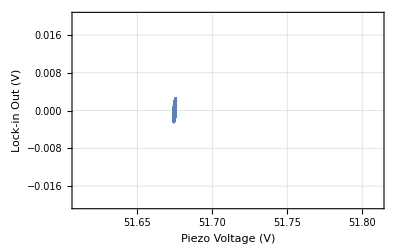
{0.094009,-Graphics-}

```mathematica
AbsoluteTiming@LaserSignalDisp[laser370]
```